```mathematica
TextRecognize[Import["/Users/adamjump/Desktop/population.tiff"]]
```

```mathematica
Import["/Users/adamjump/tmp/data.csv"] //TableForm
```

Year | Population
1790 | 3929000
1800 | 5308000
1810 | 7240000
1820 | 9638000
1830 | 12866000
1840 | 17069000
1850 | 23192000
1860 | 31443000
1870 | 38558000
1880 | 50156000
1890 | 62948000
1900 | 75995000
1910 | 91972000
1920 | 105711000
1930 | 122755000
1940 | 131669000
1950 | 150697000
1960 | 179323000
1970 | 203212000
1980 | 226505000
1990 | 248710000
2000 | 281416000
2010 | 308746000

```mathematica
Length[{{"Year", "Population"}, {1790, 3929000}, {1800, 5308000}, {1810, 7240000}, {1820, 9638000}, {1830, 12866000}, {1840, 17069000}, {1850, 23192000}, {1860, 31443000}, {1870, 38558000}, {1880, 50156000}, {1890, 62948000}, {1900, 75995000}, {1910, 91972000}, {1920, 105711000}, {1930, 122755000}, {1940, 131669000}, {1950, 150697000}, {1960, 179323000}, {1970, 203212000}, {1980, 226505000}, {1990, 248710000}, {2000, 281416000}, {2010, 308746000}}]
```

24

```mathematica
Table[%385[[i,2]],{i,2,24}]
```

{3929000,5308000,7240000,9638000,12866000,17069000,23192000,31443000,38558000,50156000,62948000,75995000,91972000,105711000,122755000,131669000,150697000,179323000,203212000,226505000,248710000,281416000,308746000}

```mathematica
Interpolation[%391]
```

InterpolatingFunction[{{1, 23}}, <>]

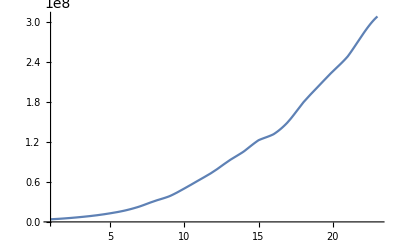

```mathematica
Plot[%392[x],{x,1,23}]
```